# Using Dodd-Frank Act Stress Test data to predict percentage growth of Microsoft Corporation stock price through 2023 Q1

Paul FischerAuthorInclude full name and credentials for all authors.Click for more information

□	Every year, the Federal Reserve publishes quarterly predictions for the following two years of domestic macroeconomic variables in both baseline and severely adverse conditions.  Historical data of these variables (also published under this act by the Federal Reserve) from 2001 to 2020 is used to make a linear regression model of Microsoft Corporation stock price percentage growth (MSFT % growth) during this period.  This model is used to predict the values of MSFT % growth under both baseline and severely adverse conditions until the end of the first quarter of 2023.  The model has an r^2 value of 0.0594964 and the predictions are qualitatively found to make inaccurate predictions of current MSFT % growth data.  I hypothesize that the inaccuracy of the model is based on the independence of the data from the macroeconomic variables and the prediction for the first two quarters of 2020 is inaccurate because the global pandemic accelerated at an unprecedented pace global dependence on Microsoft Corporation technology. AbstractAn abstract summarizes the most important points in your essay.
	◼ Summarize your most important content in about 100 words.
	◼ Provide a concise overview of the essay's conversation.
	◼ Highlight the motivations and scope.
	◼ Pay attention to the target audience.

Example:
Public-key cryptography, also known as asymmetric cryptography, uses two different but mathematically linked keys, one public and one private. In Rivest–Shamir–Adleman (RSA) cryptography, both the public and the private keys can encrypt a message; the opposite key from the one used to encrypt a message is used to decrypt it. Using RSA, we show how to encrypt messages between two users.
Click for more information

## IntroductionSectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more information

Movements of the stock market are famously hard to predict, but clever data science researchers continue to make breakthroughs in this regard that make hedge funds billions of dollars (USD) every year.  One of the most common problems data scientists run into when making predictive models is overfitting.  Making a linear regression model of too many (possibly dependent) variables usually leads to models that seem accurate with respect to the training data set but make poor predictions on the testing data set(s) ["[1]"](https://www.investopedia.com/terms/o/overfitting.asp).  
	Every year, according to the Dodd-Frank Act, the Federal Reserve publishes predictions of macroeconomic variables (i.e. real GDP growth, unemployment rate, etc.) for the following two years under baseline and severely adverse conditions in an attempt to prevent a financial crisis (like the one of 2008) ["[2]"](https://www.investopedia.com/terms/d/dodd-frank-financial-regulatory-reform-bill.asp).  In section "Data Wrangling" of this computational essay, I will gather into a Wolfram Language DataSet the historic domestic stress test data from 2001 to 2020 published on the ["Federal Reserve website"](https://www.federalreserve.gov/supervisionreg/dfa-stress-tests.htm) as well as the historic Microsoft Corporation stock price percentage growth (MSFT % growth) data during this period and wrangle the data until the data can be plotted via the built-in Wolfram Language function DateListPlot.  In section "Linear Regression Model", the Pearson correlation coefficients will be calculated between each variable and the MSFT % growth data, and the variable(s) clustered together by highest correlation will be used to make a linear regression model of the data according to a least squares linear model fit.  Only the variables clustered together by highest correlation will be used in an attempt to prevent overfitting.  In section "Predictions", the linear model fit will be used to project the MSFT % growth data until 2023 using both the baseline and severely affected stress test predictions, and these will be compared to the current MSFT % growth data (as of 2020 Q2).  Finally, in section "Summary and Conclusions", I will summarize the results and provide suggestions for further research.

## Data WranglingSectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more information

We begin our investigation by importing as a Wolfram Language Dataset quarterly time series data of historic domestic macroeconomic variables from the Dodd-Frank Supervisory Stress Test published as a CSV file on the Federal Reserve website.  We can observe the different variables we have to work with in the columns below.

```mathematica
histDmstc=
Dataset[Import["https://www.federalreserve.gov/supervisionreg/files/2020-historical-data.zip","Historic_Domestic.csv"
]
]
```

The first format specified by the Wolfram Language & System Documentation Center for the function DateListPlot is as follows: 

DateListPlot[{{date1,v1},{date2,v2},...}].  

We need to clean the data so that we can have the right format to, for example, use the second and third columns of the Dataset to make a DateListPlot for Real GDP growth.  We can begin by turning the dates into a format that can be turned into a Wolfram Language DateObject.  We create the function dateCleaner below for this purpose.

```mathematica
dateCleaner[dirtyDate_] := StringReplace[
dirtyDate,
{"Q1"->"Mar 31","Q2"->"June 30","Q3"->"September 30","Q4"->"December 31"}
]
```

Now that we have a function that can put the dates into the format we want to create a date object, we can set the rows that it will start and finish on (so that we can decide later if there is a specific period from the data we want to take).

```mathematica
startDate=Position[histDmstc[[All,2]],"2001 Q1"][[1,1]]
```

102

```mathematica
totalRows=Length[histDmstc[[All,1]]]
```

177

In this case, we want to make a linear regression model for MSFT % growth.  However, we can see from the graph below that the period leading up to 2000, the famous dot-com bubble, is an anomaly that will affect the accuracy of our model’s ability to predict future stock prices.  For this reason, we will create a model that fits the data after 2001.

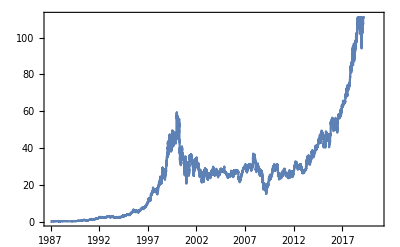

```mathematica
DateListPlot[FinancialData["MSFT","1987"]]
```

Since the historic domestic macroeconomic variable is given as a function of quarters, we create an array that contains the end date of each quarter that we’re interested in using to train our model and observe its length.

```mathematica
quarterEndDates=Normal[dateCleaner/@histDmstc[[All,2]][[startDate;;totalRows]]];
Print[quarterEndDates[[1]]]
```

2001 Mar 31

```mathematica
Print[Length[quarterEndDates]]
```

76

Since we are plotting % growth, as opposed to strictly the stock price, we need to include the price from the end of the previous quarter.  We use a for loop to create a time series array that lists the date objects and corresponding stock price for each quarter, and then we write a for loop after that to calculate the % growth from the previous quarter to the current one.  We can observe the plot of MSFT % growth from 2001 to 2020 below.

```mathematica
msftQuarterEndDates=Normal[dateCleaner/@histDmstc[[All,2]][[startDate-1;;totalRows]]];
Print[msftQuarterEndDates[[1]]]
```

2000 December 31

```mathematica
msftPriceData = ConstantArray[0,Length[msftQuarterEndDates]];
For[
i=1,i≤Length[msftQuarterEndDates],i++,
msftPriceData[[i]]={DateObject[msftQuarterEndDates[[i]]],QuantityMagnitude@FinancialData["MSFT",{msftQuarterEndDates[[i]]}]}
]
Print[msftPriceData[[1;;10,All]]]
```

{{Day: Sun 31 Dec 2000,21.688},{Day: Sat 31 Mar 2001,27.344},{Day: Sat 30 Jun 2001,36.5},{Day: Sun 30 Sep 2001,25.585},{Day: Mon 31 Dec 2001,33.135},{Day: Sun 31 Mar 2002,30.155},{Day: Sun 30 Jun 2002,27.35},{Day: Mon 30 Sep 2002,21.87},{Day: Tue 31 Dec 2002,25.85},{Day: Mon 31 Mar 2003,24.21}}

```mathematica
(* msftData refers to the data that will be used -- MSFT % growth *)
(* originally the stock price was used, but I switched to plotting % growth because it had a higher Pearson correlation coefficient with respect to the variables *)
msftData=ConstantArray[0,Length[quarterEndDates]];
For[
i=1,i≤Length[quarterEndDates],i++,
msftData[[i]]={DateObject@quarterEndDates[[i]],msftPriceData[[i+1,2]]/msftPriceData[[i,2]]-1}
]
Print[msftData[[1;;10,All]]]
```

{{Day: Sat 31 Mar 2001,0.260789},{Day: Sat 30 Jun 2001,0.334845},{Day: Sun 30 Sep 2001,-0.299041},{Day: Mon 31 Dec 2001,0.295095},{Day: Sun 31 Mar 2002,-0.089935},{Day: Sun 30 Jun 2002,-0.0930194},{Day: Mon 30 Sep 2002,-0.200366},{Day: Tue 31 Dec 2002,0.181984},{Day: Mon 31 Mar 2003,-0.063443},{Day: Mon 30 Jun 2003,0.0590665}}

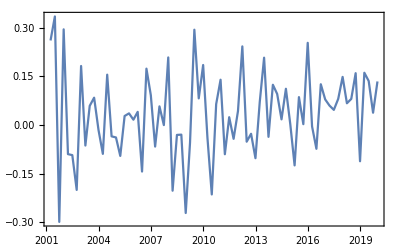

```mathematica
DateListPlot[msftData,PlotLegends->"MSFT % growth"]
```

We now create a series of nested functions leading to the parent function plottableDataColumn which returns a list containing the time series data in the proper format to be used as input for the DateListPlot function.  Below we set up all of the lists of macroeconomic variables using this function in the format we desire.  We can observe the example below of plotting the real GDP growth and the MSFT % growth from 2001 to 2020.

```mathematica
nestListMaker[macroVar_,col_,startD_,totalR_]:=Normal[{dateCleaner/@macroVar[[All,2]][[startD;;totalR]],macroVar[[startD;;totalR,col]]}]
assocMaker[nestList_]:=AssociationThread[DateObject/@nestList[[1]],nestList[[2]]]
plottableMacroVar[assoc_]:=Flatten/@List@@@Normal@assoc
plottableDataColumn[csvData_,col_,startD_,totalR_]:=plottableMacroVar[assocMaker[nestListMaker[csvData,col,startD,totalR]]]
```

```mathematica
(* Real GDP growth *)
realGdpGrowth=plottableDataColumn[histDmstc,3,startDate,totalRows]; 

 (* Nominal GDP growth *)
nomGdpGrowth=plottableDataColumn[histDmstc,4,startDate,totalRows];

(* Real disposable income growth *)
realDispIncGrowth=plottableDataColumn[histDmstc,5,startDate,totalRows]; 

(* Nominal disposable income growth *)
nomDispIncGrowth=plottableDataColumn[histDmstc,6,startDate,totalRows]; 

(* Unemployment rate *)
unEmpRate=plottableDataColumn[histDmstc,7,startDate,totalRows];

(* CPI inlfation rate *)
cpiInfRate=plottableDataColumn[histDmstc,8,startDate,totalRows];

(* 3-month Treasury rate *)
treasRate3Mo=plottableDataColumn[histDmstc,9,startDate,totalRows];

(* 5-year Treasury yield (Already created above) *)
treasYield5Yr=plottableDataColumn[histDmstc,10,startDate,totalRows];
```

{{Day: Sat 31 Mar 2001,-1.1},{Day: Sat 30 Jun 2001,2.4},{Day: Sun 30 Sep 2001,-1.6},{Day: Mon 31 Dec 2001,1.1},{Day: Sun 31 Mar 2002,3.5},{Day: Sun 30 Jun 2002,2.4},{Day: Mon 30 Sep 2002,1.8},{Day: Tue 31 Dec 2002,0.6},{Day: Mon 31 Mar 2003,2.2},{Day: Mon 30 Jun 2003,3.5}}

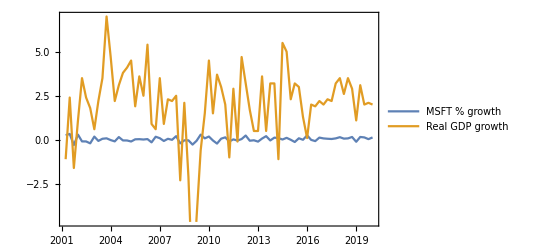

```mathematica
Print[realGdpGrowth[[1;;10,All]]]
DateListPlot[{msftData,realGdpGrowth},PlotLegends->{"MSFT % growth","Real GDP growth"}]
```

Below we can observe qualitatively how the different variables correlate with each other.

```mathematica
vars={msftData,realGdpGrowth,nomGdpGrowth,realDispIncGrowth,nomDispIncGrowth,unEmpRate,cpiInfRate,treasRate3Mo,treasYield5Yr};
```

```mathematica
varLabels={"MSFT % growth","Real GDP growth","Nominal GDP growth","Real disposable income growth","Nominal disposable income growth","Unemployment rate","CPI inlfation rate","3-month Treasury rate","5-year Treasury yield"};
```

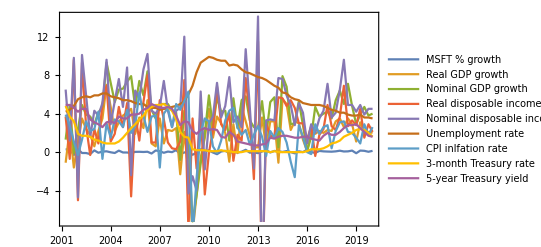

```mathematica
DateListPlot[vars,PlotLegends->varLabels]
```

## Linear Regression ModelSectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more information

Now that we have wrangled the data into the format we want, let's observe which macroeconomic variables best correlate with the MSFT % growth data.  Here we use a for loop to create an association between each variable and it's correlation so that it is easy for us to visually see the results.  Then we use the Find Clusters function to find which variable(s) have the highest correlation.

```mathematica
correlAssoc=ConstantArray[0,8];
For[
i=2,i≤9,i++,
correlAssoc[[i-1]]=varLabels[[i]]->Abs[Correlation[msftData[[All,2]],vars[[i,All,2]]]]
]
highestCorrel=Sort[Association@correlAssoc,Greater]
```

<|Real GDP growth→0.243919,Nominal GDP growth→0.182107,CPI inlfation rate→0.166155,Real disposable income growth→0.123978,Unemployment rate→0.0761084,Nominal disposable income growth→0.0523073,3-month Treasury rate→0.0458761,5-year Treasury yield→0.0413313|>

```mathematica
clust=FindClusters[highestCorrel]
```

{{Real GDP growth},{Nominal GDP growth,CPI inlfation rate},{Real disposable income growth},{Unemployment rate,Nominal disposable income growth,3-month Treasury rate,5-year Treasury yield}}

We can see that the Real GDP growth had the highest correlation to the data, high enough to put it into its own cluster.  The Pearson Correlation Coefficient is only 0.243919, which is smaller than we would want to see and means that our final linear regression model will not be as accurate as we hope it will be.  

Regardless, the next step for us is to use the built-in Wolfram Language LeastSquares function to find the coefficients that best fit a linear regression model of this variable to the MSFT % growth data.  We can observe the plot below of the model, and the plot below it of how the model fits the MSFT data.  While the model doesn't fit the peaks and valleys of the MSFT data perfectly, it does qualitatively seem to follow some of the main trends and is bounded by its extrema.  This is illustrated by the plot below it that includes the real GDP growth variable that was used to make the model.  We can observe that we end up with an r^2 value of 0.0594964 which is much lower than we were hoping to see for our model to be tightly correlated to the data.

```mathematica
mat=Transpose[{realGdpGrowth[[All,2]],ConstantArray[1,Length[quarterEndDates]]}];
coeffs=LeastSquares[mat,msftData[[All,2]]];
AssociationThread[{"Real GDP growth","Y-intercept"},coeffs]
```

<|Real GDP growth→0.0141005,Y-intercept→0.00665531|>

```mathematica
linModFitVec=mat.coeffs;
linModFitAssoc=AssociationThread[msftData[[All,1]],linModFitVec];
linModFit=Flatten/@List@@@Normal@linModFitAssoc;
Print[linModFit[[1;;10]]]
```

{{Day: Sat 31 Mar 2001,-0.00885529},{Day: Sat 30 Jun 2001,0.0404966},{Day: Sun 30 Sep 2001,-0.0159056},{Day: Mon 31 Dec 2001,0.0221659},{Day: Sun 31 Mar 2002,0.0560072},{Day: Sun 30 Jun 2002,0.0404966},{Day: Mon 30 Sep 2002,0.0320363},{Day: Tue 31 Dec 2002,0.0151156},{Day: Mon 31 Mar 2003,0.0376765},{Day: Mon 30 Jun 2003,0.0560072}}

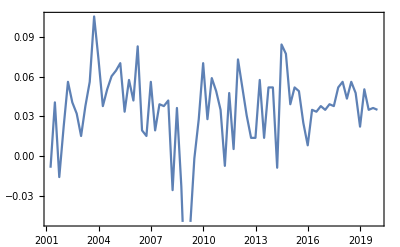

```mathematica
DateListPlot[linModFit]
```

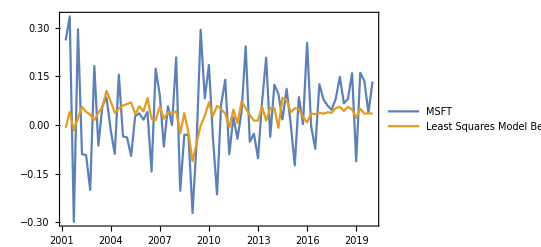

```mathematica
DateListPlot[{msftData,linModFit},PlotLegends->{"MSFT","Least Squares Model Best Fit"}]
```

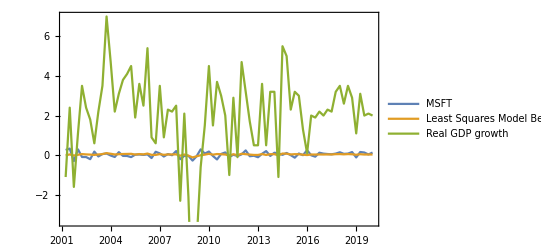

```mathematica
DateListPlot[{msftData,linModFit,realGdpGrowth},PlotLegends->{"MSFT","Least Squares Model Best Fit","Real GDP growth"}]
```

```mathematica
rSquared=Correlation[msftData[[All,2]],linModFit[[All,2]]]^2
```

0.0594964

Now that we have a model, albeit an inaccurate one, we can use it to predict the future MSFT % growth based on the Federal Reserves' prediction of the macroeconomic variables.

## PredictionsSectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more information

Now we import the Federal Reserves' predictions for the future of the variables that we used before.  They have a baseline prediction and a severely affected prediction.  We will see how both compare to the actual 2020 data that has come in so far.  Below we can see the plot of the baseline and a plot of the severely adverse prediction for real GDP growth for 2020 to 2023.  The columns can be seen by clicking on the first cell of the output below.

```mathematica
baseDmstc =
Dataset[
Import["https://www.federalreserve.gov/supervisionreg/files/2020-macro-scenario-tables.zip","Table_2A_Supervisory_Baseline_Domestic.csv"
]
]
```

```mathematica
severeDmstc=
Dataset[Import["https://www.federalreserve.gov/supervisionreg/files/2020-macro-scenario-tables.zip","Table_3A_Supervisory_Severely_Adverse_Domestic.csv"
]
];
baseFutRealGdp=plottableDataColumn[baseDmstc,3,2,14]; 
sevFutRealGdp=plottableDataColumn[severeDmstc,3,2,14];
```

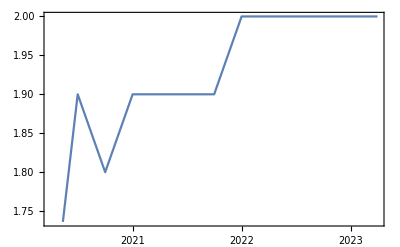

```mathematica
DateListPlot[baseFutRealGdp,PlotLegends->"Supervisory Baseline Domestic Real GDP growth"]
```

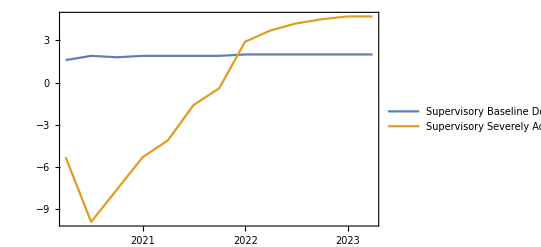

```mathematica
DateListPlot[{baseFutRealGdp,sevFutRealGdp},PlotLegends->{"Supervisory Baseline Domestic Real GDP growth","Supervisory Severely Adverse Domestic Real GDP Growth"}]
```

We use the coefficients of the linear fit model from before to make a new model for the predicted values.

```mathematica
msftPredictionBase=ConstantArray[0,13];
msftPredictionSevere=ConstantArray[0,13];
For[
i=1,i≤13,i++,
msftPredictionBase[[i]]={baseFutRealGdp[[i,1]],0.014100544867108404*baseFutRealGdp[[i,2]]+0.0066553136085142515};
msftPredictionSevere[[i]]={baseFutRealGdp[[i,1]],0.014100544867108404*sevFutRealGdp[[i,2]]+0.0066553136085142515};
]
```

Then we use the process we used before to get the current 2020 MSFT % growth data per quarter.

```mathematica
msftPresentQuarterEndDates=Flatten[{"2019 Dec 31",Normal[dateCleaner/@baseDmstc[[All,2]][[2;;3]]]}]
```

{2019 Dec 31,2020 Mar 31,2020 June 30}

```mathematica
msftPresentPriceData = ConstantArray[0,Length[msftPresentQuarterEndDates]];
For[
i=1,i≤Length[msftPresentQuarterEndDates],i++,
msftPresentPriceData[[i]]={DateObject[msftPresentQuarterEndDates[[i]]],QuantityMagnitude@FinancialData["MSFT",{msftPresentQuarterEndDates[[i]]}]}
]
Print[msftPresentPriceData]
```

{{Day: Tue 31 Dec 2019,157.7},{Day: Tue 31 Mar 2020,157.71},{Day: Tue 30 Jun 2020,203.51}}

```mathematica
msftPerGrowth=ConstantArray[0,Length[msftPresentQuarterEndDates]-1];
For[
i=1,i≤Length[msftPresentQuarterEndDates]-1,i++,
msftPerGrowth[[i]]={DateObject@msftPresentQuarterEndDates[[i+1]],msftPresentPriceData[[i+1,2]]/msftPresentPriceData[[i,2]]-1}
]
Print[msftPerGrowth]
```

{{Day: Tue 31 Mar 2020,0.0000634735},{Day: Tue 30 Jun 2020,0.290406}}

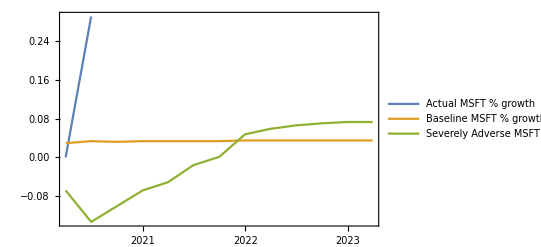

```mathematica
DateListPlot[{msftPerGrowth,msftPredictionBase,msftPredictionSevere},PlotLegends->{"Actual MSFT % growth","Baseline MSFT % growth prediction","Severely Adverse MSFT % growth prediction"}]
```

In the plot above, we can see that neither prediction seems to match the 2020 data well.  This may be because the increase in technological use during the coronavirus caused the stock price to rise, despite the unprecedented fall in the national GDP.  The correlations below are 1 because we have only observed the first 2 quarters of 2020, and these values can be updated as we get to the end of 2023 and see how well our predictive model correlates with how the stock performs.

```mathematica
rSquaredBase=Correlation[msftPerGrowth[[All,2]],msftPredictionBase[[1;;2,2]]]^2
```

1.

```mathematica
rSquaredSevere=Correlation[msftPerGrowth[[All,2]],msftPredictionSevere[[1;;2,2]]]^2
```

1.

## Summary and ConclusionsSectionHeaderInfoButtonA proper heading structure helps to organize your content for readability. ◼ Categorize sections based on similar content. ◼ Each section should tell a story by itself. ◼ Headings overall should tell the outline of the essay. Examples: The Central Limit Theorem Discovering the Central Limit Theorem The Normal Distribution Toward the Normal Distribution The Normal Distribution in 2D and Beyond Random Walks What Is Not a Normal Distribution Collapse Models Collapse Problem in Quantum Random Processes Collapse as a Dynamical Random Process Recovering Quantum after Statistical Averaging Drawbacks of Collapse Models Click for more information

The linear regression model meant to fit the smallest number of macroeconomic variables possible from the Dodd-Frank Act Stress Test data didn't predict the historic domestic data as well as I had hoped.  This may be because MSFT data is better correlated to other variables besides the ones included in the stress test data.  I believe the current 2020 data doesn't qualitatively fit either prediction because the coronavirus created an unprecedented dependence on Microsoft Corporation technology despite the fall in the GDP.  In the future I would like to see how more variables, neural networks with LSTM layers, and transformations and lags of the variables will make predictions that better correlate with the data.

## KeywordsKeywordsInfoButtonList relevant terms that should be used to include the essay in search results.Click for more information

Dodd-Frank Act Stress Test

Federal Reserve

Microsoft Corporation stock price percentage growth

Overfitting

Linear Regression